```mathematica
c=Length[DictionaryLookup[#~~___,IgnoreCase->True]]&/@CharacterRange["a","z"]
```

{5305,5510,8726,5647,3607,3757,3096,3466,3569,1017,928,2913,5190,2021,2320,7130,450,5572,10474,4664,2647,1405,2492,46,331,224}

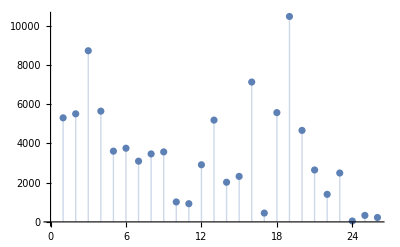

```mathematica
ListPlot[%,Filling->Axis]
```

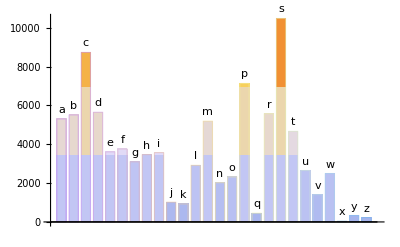

```mathematica
BarChart[c,ChartLabels->Placed[CharacterRange["a","z"],Above],ChartStyle->"Pastel",ChartElementFunction->"GradientScaleRectangle"]
```

```mathematica
data=DictionaryLookup["*"];
c={};
Do[
If[data[[i]]==StringReverse[data[[i]]],
AppendTo[c,data[[i]]]],{i,1,Length[data]}];
c
```

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

```mathematica
DictionaryLookup[x___/;x==StringReverse[x]]
```

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

```mathematica
c={};
time=First@Timing[For[j=1,j≤26,j++,firstletterlist=DictionaryLookup[#~~___]&@CharacterRange["a","z"]⟦j⟧;
lastletterlist=DictionaryLookup[___~~#]&@CharacterRange["a","z"]⟦j⟧;
length=Length[firstletterlist];
For[i=1,i≤length,i++,currentWord=firstletterlist⟦i⟧;
If[MemberQ[lastletterlist,StringReverse[currentWord]],AppendTo[c,currentWord]]]]];
{time,Length[c],c//Short}
```

{11.2526,487,{a,abut,agar,«482»,yaws,yob}}

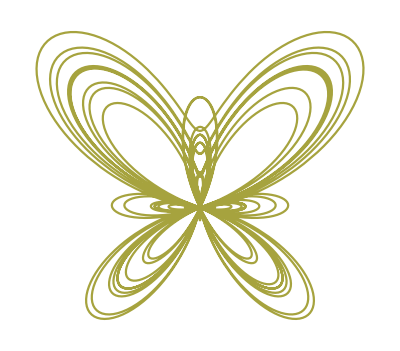

```mathematica
ParametricPlot[{Sin[t](E^Cos[t]-2Cos[4t]+Sin[1/12 t]^5),Cos[t](E^Cos[t]-2Cos[4t]+Sin[1/12 t]^5)},{t,0,20π},Axes->False,ColorFunction->Function[{x,y},Hue[y^2]]]
```

```mathematica
langs=Select[DictionaryLookup[All],Not[SameQ[#,"Hebrew"]]&];
dicts=Map[DictionaryLookup[{#,"*"}]&,langs];
palis=Map[Intersection[#,StringReverse[#]]&,dicts];
letts=Quiet@Map[DeleteDuplicates[StringTake[#,1]]&,palis];
lists=Transpose[{langs,letts}];
```

```mathematica
palindromeEng[lang_,lowerLetterRange_]:=Module[{dict,lowerCasePalindrome,letterLength,searchLetter,palindromeLetter,dictLetter},dict=DictionaryLookup[{lang,"*"}];
lowerCasePalindrome=Intersection[ToLowerCase[dict],StringReverse[ToLowerCase[dict]]];
letterLength=Length[lowerLetterRange];
Flatten@Table[searchLetter=lowerLetterRange⟦i⟧;palindromeLetter=Select[lowerCasePalindrome,StringTake[#,1]===searchLetter&];
dictLetter=DictionaryLookup[{lang,StringJoin[searchLetter,"*"]},IgnoreCase->True];
Select[dictLetter,Or@@StringMatchQ[palindromeLetter,ToLowerCase[#]]&],{i,1,letterLength}]];
```

```mathematica
palindrome[lang_]:=If[lang==="English",palindromeEng["English",CharacterRange["a","z"]],With[{dict=DictionaryLookup[{lang,"*"}]},Intersection[dict,StringReverse[dict]]]];
```

```mathematica
language="English";
```

```mathematica
lettersList={{"English",Union[CharacterRange["a","z"],CharacterRange["A","Z"]]},{"Dutch",{"a","b","c","d","e"}}};
```

```mathematica
Manipulate[(*load palindrome search only if laguage changed*)
workingPalindrome=If[!SameQ[language,currentLang],
currentLang=language;palindrome[language],workingPalindrome];
Module[{letterClass,oneWord,twoWords,twoWordsHalf,twoWordsPair,fitOneWord,fitTwoWords,gridOneWord,gridTwoWords},
(*Select letter navigated words*)
letterClass=Select[workingPalindrome,StringMatchQ[#,letter~~___]&];
(*classify into one word and two words*)
oneWord=Select[letterClass,(ToLowerCase[#]===ToLowerCase[StringReverse[#]])&;
twoWords=Complement[letterClass,oneWord];
twoWordsHalf=If[language==="English",Flatten@Table[Select[Nearest[workingPalindrome,ToLowerCase[StringReverse[twoWords⟦i⟧]],300],(ToLowerCase[#]===ToLowerCase[StringReverse[twoWords⟦i⟧]])&,1],{i,1,Length[twoWords]}],None];
twoWordsPair=If[language==="English",Transpose[{twoWords,twoWordsHalf}],Transpose[{twoWords,StringReverse[twoWords]}]];
(*rearrange table*)
fitOneWord=PadRight[oneWord,10*(Floor[(Length[oneWord]-1)/10]+1),Null];
fitTwoWords=PadRight[twoWordsPair,4*(Floor[(Length[twoWordsPair]-1)/4]+1),Null];
gridOneWord=Grid[Partition[If[language==="English",Map[Button[#,Speak[#],Appearance->None]&,fitOneWord],fitOneWord],10],Background->LightBlue];
gridTwoWords=Grid[Partition[If[language==="English",Map[Button[#,Speak[#],Appearance->None]&,fitTwoWords],fitTwoWords],4],Background->LightGreen];
(*Show on table form*)
Text@Column[{Style[Row[{"letter:",letter}],Bold,12],Style[Row[{"total palindrome words:",Length[workingPalindrome],If[language==="English","   tips :click on word → read it aloud"]}],Bold,12],
TableForm[{gridOneWord,gridTwoWords},TableHeadings->{{Row[{Length[oneWord]," one-word",If[Length[oneWord]≤1," "," "]}],Row[{Length[twoWordsPair]," two-word ",If[Length[twoWordsPair]≤1," "," "]}]},None}]},Alignment->Left]]],
Row[{Control[{{language,"English","language"},Cases[DictionaryLookup[All],Except["Hebrew"]],ControlType->PopupMenu}],
Control[{{letter,"e","  letter"},Last@Flatten[Select[lettersList,(#⟦1⟧===language)&],1],ControlType->Manipulator,ImageSize->Small}]}],
ControlPlacement->Top,TrackedSymbols->True,SaveDefinitions->True]
```

Complement::normal: Complement[«1»] 中的位置 2 处应该是非原子表达式.

StringReverse::string: StringReverse[Complement[{e,ec,efeb,egua,eh,ela,elet,elev,«16»,erros,es,essiu,et,eugasser,evoc,ex},«13»]] 中位置 1 处应该是字符串.

Transpose::nmtx: {Complement[{e,ec,efeb,egua,eh,ela,elet,elev,«15»,erres,erros,es,essiu,et,eugasser,evoc,ex},«13»],«1»} 的前两层无法转置.

PadRight::normal: PadRight[oneWord$37439,0,Null] 中的位置 1 处应该是非原子表达式.

Transpose::nonopt: Transpose[«1»] 中位置 2 外应该是选项（而不是 Null）. 选项必须是一个规则或者规则列表.

PadRight::argb: 调用 PadRight 时使用了 0 个参数；应该用 1 到 4 个参数.

Transpose::nonopt: Transpose[«1»] 中位置 2 外应该是选项（而不是 Null）. 选项必须是一个规则或者规则列表.

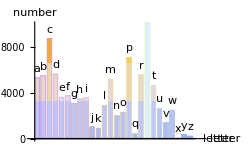
-Graphics-
图4-1 英语中首字母的分布图

```mathematica
(*第二次学习*)
wordLength=Length[DictionaryLookup[#~~__,IgnoreCase->True]]&/@CharacterRange["a","z"];
Column[{BarChart[wordLength,PlotRange->{{0,28},{0,10000}},ImageSize->250,AxesLabel->{"letter","number"},ChartLabels->Placed[CharacterRange["a","z"],Above],ChartElementFunction->"GradientScaleRectangle",ChartStyle->"Pastel"],Text@Style["图4-1 英语中首字母的分布图"]},Alignment->Center]
```